The equations below have to do with the energy inputted to the system by the “East Sun” and the “South Sun”.

```mathematica
Subscript[height, U] = 3.40 (*the distance to the top of the upper floor from the bottom of the awning*)
Subscript[height, L] = 4.95 (*the distance to the top of the lower floor from the bottom of the awning*)
```

3.4

4.95

```mathematica
lengthAwning = 5.38
epsilon = 0.7 (*emmisivity*)
sigma = 5.670*10^(-8) (*Stefan-Boltzmann constant*)
Subscript[theta, o] = 0.01 (*initial angle of the sun*)
```

5.38

0.7

5.67×10^-8

0.01

```mathematica
Subscript[A, sunsouth] = 36.14 (*area of the south windows*) 
Subscript[c, floor] = 1850(*specific heat of the floor*)
Subscript[A, endcap] = 53.9(*area of the floor in the endcap*)
Subscript[A, middle] = 372.31(*area of the floor in the middle*)
Subscript[h, floortoair] = 10 (*heat transfer coefficient of the floor to air*)
Subscript[h, airtoair] = 50 (*heat transfer coefficient between air*)
Subscript[A, crosssect] = 13.40 (*area of the vertical cross section of one floor in the AC*)
Subscript[A, glassendcap] = 36.14
Subscript[m, floor] = 1.52*Subscript[A, middle] * 615.5 (*mass of the upper floor*)
Subscript[A, glassmiddle] = 498.48 (*area of the glass facing east in one floor in the middle of the ac*)
Subscript[h, glass] = 0.7 (*lumped resistance for the convection to glass, conduction through glass, and convection to the outside world*)
Subscript[T, out] = 12 (*assuming there is a constant temperature outside*)
Subscript[m, endcapair] = 3.4*Subscript[A, endcap]*1.225 (*mass of the air in one floor of the endcap*)
Subscript[m, middleair] = 3.4*Subscript[A, endcap]*1.225  (*mass of the air in one floor of the middle AC*)
Subscript[c, air] = 1006(*specific heat of air*)
```

36.14

1850

53.9

372.31

10

50

13.4

36.14

348318.

498.48

0.7

12

224.494

224.494

1006

```mathematica
Subscript[theta, ang][t_]=((90/325)*t + Subscript[theta, o]) (*angle of the elevation of the sun*)
Subscript[A, suneastu][t_]=(Subscript[height, U]-(lengthAwning/(Tan[ (90-Subscript[theta, ang][t])Degree]))/Tan[(Subscript[theta, ang][t])Degree]) (*areas of the floor that is covered by the sun*)
Subscript[A, suneastl][t_]=(Subscript[height, L]-(lengthAwning/(Tan[(90-Subscript[theta, ang][t])Degree]))/Tan[(Subscript[theta, ang][t])Degree])

Subscript[Watt, u][t_]=epsilon*sigma*Subscript[T, u][t]^4 (*power put into the system by the sun on both floors*)
Subscript[Watt, l][t_]=epsilon*sigma*Subscript[T, l][t]^4
```

0.01+(18 t)/65

3.4-5.38 Cot[° (89.99-(18 t)/65)] Cot[° (0.01+(18 t)/65)]

4.95-5.38 Cot[° (89.99-(18 t)/65)] Cot[° (0.01+(18 t)/65)]

3.969×10^-8 T_u[t]^4

3.969×10^-8 T_l[t]^4

```mathematica
(*Subscript[Q, suneastu][t_]=Piecewise[{{Subscript[Watt, u][t] * Subscript[A, suneastu][t],{0<t<325}}}] (*equations that define the sun input until noon*)
Subscript[Q, suneastl][t_]=Piecewise[{{Subscript[Watt, l][t] * Subscript[A, suneastl][t],{0<t<325}}}]

Subscript[Q, sunsouthu][t_] = Piecewise[{{Subscript[Watt, u][t] * Subscript[A, sunsouth],{325<t<650}}}](*equations that defind the sun input from noon to sunset*)
Subscript[Q, sunsouthl][t_] = Piecewise[{{Subscript[Watt, l][t] * Subscript[A, sunsouth],{325<t<650}}}]*)
```

```mathematica
Subscript[Q, suneastu1][t_]=Subscript[Watt, u][t] * Subscript[A, suneastu][t](*equations that define the sun input until noon*)
Subscript[Q, suneastl1][t_]=Subscript[Watt, l][t] * Subscript[A, suneastl][t]

Subscript[Q, sunsouthu1][t_] = 0 (*equations that defind the sun input from noon to sunset*)
Subscript[Q, sunsouthl1][t_] = 0
```

3.969×10^-8 (3.4-5.38 Cot[° (89.99-(18 t)/65)] Cot[° (0.01+(18 t)/65)]) T_u[t]^4

3.969×10^-8 (4.95-5.38 Cot[° (89.99-(18 t)/65)] Cot[° (0.01+(18 t)/65)]) T_l[t]^4

0

0

```mathematica
Subscript[Q, suneastu2][t_]=0(*equations that define the sun input until noon*)
Subscript[Q, suneastl2][t_]=0

Subscript[Q, sunsouthu2][t_] = Subscript[Watt, u][t] * Subscript[A, sunsouth] (*equations that defind the sun input from noon to sunset*)
Subscript[Q, sunsouthl2][t_] = Subscript[Watt, l][t] * Subscript[A, sunsouth]
```

0

0

1.4344×10^-6 T_u[t]^4

1.4344×10^-6 T_l[t]^4

```mathematica
(*Subscript[Q, suneastu][t_]=Subscript[Watt, u][t] * Subscript[A, suneastu][t] (*equations that define the sun input from sunrise til until noon (0<=t<=325*)
Subscript[Q, suneastl][t_]=Subscript[Watt, l][t] * Subscript[A, suneastl][t]
Subscript[Q, sunsouthu][t_] = 0
Subscript[Q, sunsouthl][t_] = 0*)
(*Subscript[Q, suneastu][t_]=0 (*equations that define the sun input from noon till sunset 325≤t≤650*)
Subscript[Q, suneastl][t_]=0

Subscript[Q, sunsouthu][t_] = Subscript[Watt, u][t] * Subscript[A, sunsouth]
Subscript[Q, sunsouthl][t_] = Subscript[Watt, l][t] * Subscript[A, sunsouth]*)
(*Subscript[Q, suneastu][t_]=0 (*equations that define the sun input from sunset to sunrise)
Subscript[Q, suneastl][t_]=0

Subscript[Q, sunsouthu][t_] = 0
Subscript[Q, sunsouthl][t_] = 0*)
```

```mathematica
(*equations that define the behavior of the components of the syatem*)
Subscript[Q, utoa][t_]=Subscript[h, floortoair]*Subscript[A, endcap]*(Subscript[T, u][t]-Subscript[T, a][t])

Subscript[Q, utob][t_] = Subscript[h, floortoair]*Subscript[A, middle] * (Subscript[T, u][t] - Subscript[T, b][t])

Subscript[Q, utoc][t_] = Subscript[h, floortoair] * Subscript[A, endcap] * (Subscript[T, u][t] - Subscript[T, c][t])

Subscript[Q, utod][t_] = Subscript[h, floortoair]*Subscript[A, middle] * (Subscript[T, u][t] - Subscript[T, d][t])

Subscript[Q, ltoc][t_] = Subscript[h, floortoair] * Subscript[A, endcap] * (Subscript[T, l][t] - Subscript[T, c][t])

Subscript[Q, ltod][t_] := Subscript[h, floortoair] * Subscript[A, endcap] * (Subscript[T, l][t] - Subscript[T, d][t])

Subscript[Q, btoa][t_] = Subscript[h, airtoair] * Subscript[A, crosssect] * (Subscript[T, b][t] - Subscript[T, a][t]) (*we are assuming that the middle will be hotter than the endcaps*)
Subscript[Q, dtoc][t_] = Subscript[h, airtoair] * Subscript[A, crosssect] * (Subscript[T, d][t] - Subscript[T, c][t])
Subscript[Q, atoout][t_] = Subscript[h, glass] * Subscript[A, glassendcap] * (Subscript[T, a][t] - Subscript[T, out])
Subscript[Q, btoout][t_] = Subscript[h, glass] * Subscript[A, glassmiddle] * (Subscript[T, b][t] - Subscript[T, out])
Subscript[Q, ctoout][t_] = Subscript[h, glass] * Subscript[A, glassendcap] * (Subscript[T, c][t] - Subscript[T, out])
Subscript[Q, dtoout][t_] = Subscript[h, glass] * Subscript[A, glassmiddle] * (Subscript[T, d][t] - Subscript[T, out])
```

539. (-T_a[t]+T_u[t])

3723.1 (-T_b[t]+T_u[t])

539. (-T_c[t]+T_u[t])

3723.1 (-T_d[t]+T_u[t])

539. (-T_c[t]+T_l[t])

670. (-T_a[t]+T_b[t])

670. (-T_c[t]+T_d[t])

25.298 (-12+T_a[t])

348.936 (-12+T_b[t])

25.298 (-12+T_c[t])

348.936 (-12+T_d[t])

The equations below describe the temperature of the upper and lower floors.

```mathematica
(*dTudt[t_]= (Subscript[Q, suneastu][t] + Subscript[Q, sunsouthu][t] -Subscript[Q, utoa][t] - Subscript[Q, utob][t] - Subscript[Q, utoc][t] - Subscript[Q, utod][t])/(Subscript[m, floor]*Subscript[c, floor])
dTldt[t_] = (Subscript[Q, suneastl][t] + Subscript[Q, sunsouthl][t] - Subscript[Q, utoc][t] - Subscript[Q, utod][t])/(Subscript[m, floor]*Subscript[c, floor])*)
(*the equations which describe from sunrise to 325*)
dTudt1[t_]= (Subscript[Q, suneastu1][t] + Subscript[Q, sunsouthu1][t] -Subscript[Q, utoa][t] - Subscript[Q, utob][t] - Subscript[Q, utoc][t] - Subscript[Q, utod][t])/(Subscript[m, floor]*Subscript[c, floor])
dTldt1[t_] = (Subscript[Q, suneastl1][t] + Subscript[Q, sunsouthl1][t] - Subscript[Q, utoc][t] - Subscript[Q, utod][t])/(Subscript[m, floor]*Subscript[c, floor])

(*the equations which describe from 325 - sunset*)
dTudt2[t_]= (Subscript[Q, suneastu2][t] + Subscript[Q, sunsouthu2][t] -Subscript[Q, utoa][t] - Subscript[Q, utob][t] - Subscript[Q, utoc][t] - Subscript[Q, utod][t])/(Subscript[m, floor]*Subscript[c, floor])
dTldt2[t_] = (Subscript[Q, suneastl2][t] + Subscript[Q, sunsouthl2][t] - Subscript[Q, utoc][t] - Subscript[Q, utod][t])/(Subscript[m, floor]*Subscript[c, floor])
```

1.55186×10^-9 (3.969×10^-8 (3.4-5.38 Cot[° (89.99-(18 t)/65)] Cot[° (0.01+(18 t)/65)]) T_u[t]^4-539. (-T_a[t]+T_u[t])-3723.1 (-T_b[t]+T_u[t])-539. (-T_c[t]+T_u[t])-3723.1 (-T_d[t]+T_u[t]))

1.55186×10^-9 (3.969×10^-8 (4.95-5.38 Cot[° (89.99-(18 t)/65)] Cot[° (0.01+(18 t)/65)]) T_l[t]^4-539. (-T_c[t]+T_u[t])-3723.1 (-T_d[t]+T_u[t]))

1.55186×10^-9 (1.4344×10^-6 T_u[t]^4-539. (-T_a[t]+T_u[t])-3723.1 (-T_b[t]+T_u[t])-539. (-T_c[t]+T_u[t])-3723.1 (-T_d[t]+T_u[t]))

1.55186×10^-9 (1.4344×10^-6 T_l[t]^4-539. (-T_c[t]+T_u[t])-3723.1 (-T_d[t]+T_u[t]))

The equations below describe the temperatures of the different air sections in the AC.

```mathematica
dTadt[t_] = (Subscript[Q, utoa][t] + Subscript[Q, btoa][t] - Subscript[Q, atoout][t])/(Subscript[m, endcapair]*Subscript[c, air])
dTbdt[t_] = (Subscript[Q, utob][t] - Subscript[Q, btoa][t] - Subscript[Q, btoout][t])/(Subscript[m, middleair]*Subscript[c, air])
dTcdt[t_] = (Subscript[Q, utoc][t] + Subscript[Q, ltoc][t] + Subscript[Q, dtoc][t] - Subscript[Q, ctoout][t])/(Subscript[m, endcapair] * Subscript[c, air])
dTddt[t_] = (Subscript[Q, utod][t] + Subscript[Q, ltod][t] -Subscript[Q, dtoc][t] - Subscript[Q, dtoout][t])/(Subscript[m, middleair] * Subscript[c, air])
```

4.4279×10^-6 (-25.298 (-12+T_a[t])+670. (-T_a[t]+T_b[t])+539. (-T_a[t]+T_u[t]))

4.4279×10^-6 (-348.936 (-12+T_b[t])-670. (-T_a[t]+T_b[t])+3723.1 (-T_b[t]+T_u[t]))

4.4279×10^-6 (-25.298 (-12+T_c[t])+670. (-T_c[t]+T_d[t])+539. (-T_c[t]+T_l[t])+539. (-T_c[t]+T_u[t]))

4.4279×10^-6 (-348.936 (-12+T_d[t])-670. (-T_c[t]+T_d[t])+539. (-T_d[t]+T_l[t])+3723.1 (-T_d[t]+T_u[t]))

Now, we will use NDSolve to generate discrete numerical approximations for all of the components.

```mathematica
(*func = NDSolve[{
Subscript[T, u]'[t] == dTudt[t],
Subscript[T, l]'[t] == dTldt[t],
Subscript[T, a]'[t] == dTadt[t],
Subscript[T, b]'[t] == dTbdt[t],
Subscript[T, c]'[t] == dTcdt[t],
Subscript[T, d]'[t] == dTddt[t],
Subscript[T, u][0]== 23,
Subscript[T, l][0] == 23,
Subscript[T, a][0] == 23,
Subscript[T, b][0] == 23,
Subscript[T, c][0] == 23,
Subscript[T, d][0] == 23
},{
Subscript[T, u][t],
Subscript[T, l][t],
Subscript[T, a][t],
Subscript[T, b][t],
Subscript[T, c][t],
Subscript[T, d][t]
},
{t,0,30}]*)

earlyfunc = NDSolve[{
Subscript[T, u]'[t] == dTudt1[t],
Subscript[T, l]'[t] == dTldt1[t],
Subscript[T, a]'[t] == dTadt[t],
Subscript[T, b]'[t] == dTbdt[t],
Subscript[T, c]'[t] == dTcdt[t],
Subscript[T, d]'[t] == dTddt[t],
Subscript[T, u][0]== 23,
Subscript[T, l][0] == 23,
Subscript[T, a][0] == 23,
Subscript[T, b][0] == 23,
Subscript[T, c][0] == 23,
Subscript[T, d][0] == 23
},{
Subscript[T, u][t],
Subscript[T, l][t],
Subscript[T, a][t],
Subscript[T, b][t],
Subscript[T, c][t],
Subscript[T, d][t]
},
{t,0.0,325.0}]
```

{{T_u[t]→InterpolatingFunction[…][t],T_l[t]→InterpolatingFunction[…][t],T_a[t]→InterpolatingFunction[…][t],T_b[t]→InterpolatingFunction[…][t],T_c[t]→InterpolatingFunction[…][t],T_d[t]→InterpolatingFunction[…][t]}}

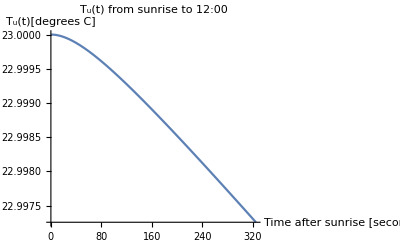

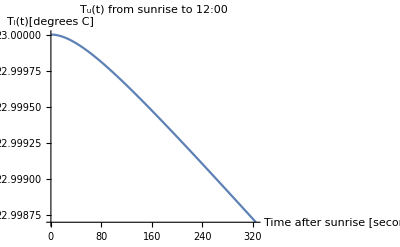

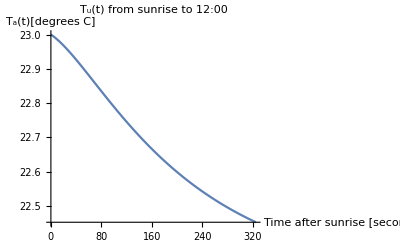

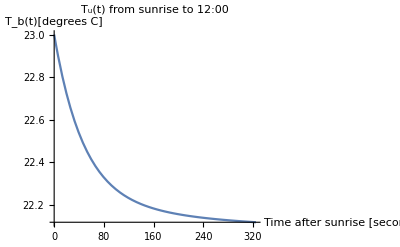

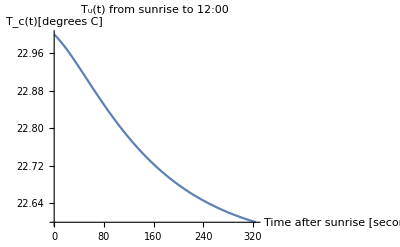

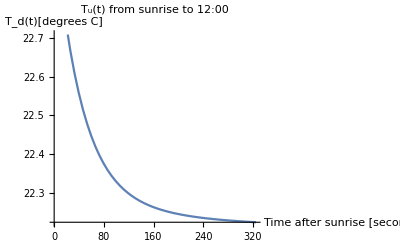

```mathematica
Plot[Subscript[T, u][t]/.earlyfunc,{t,0,325},PlotLabel->"T_u(t) from sunrise to 12:00", AxesLabel-> {"Time after sunrise [seconds]","T_u(t)[degrees C]"}]
Plot[Subscript[T, l][t]/.earlyfunc,{t,0,325},PlotLabel->"T_u(t) from sunrise to 12:00", AxesLabel-> {"Time after sunrise [seconds]","T_l(t)[degrees C]"}]
Plot[Subscript[T, a][t]/.earlyfunc,{t,0,325},PlotLabel->"T_u(t) from sunrise to 12:00", AxesLabel-> {"Time after sunrise [seconds]","T_a(t)[degrees C]"}]
Plot[Subscript[T, b][t]/.earlyfunc,{t,0,325},PlotLabel->"T_u(t) from sunrise to 12:00", AxesLabel-> {"Time after sunrise [seconds]","T_b(t)[degrees C]"}]
Plot[Subscript[T, c][t]/.earlyfunc,{t,0,325},PlotLabel->"T_u(t) from sunrise to 12:00", AxesLabel-> {"Time after sunrise [seconds]","T_c(t)[degrees C]"}]
Plot[Subscript[T, d][t]/.earlyfunc,{t,0,325},PlotLabel->"T_u(t) from sunrise to 12:00", AxesLabel-> {"Time after sunrise [seconds]","T_d(t)[degrees C]"}]
```

```mathematica
latefunc = NDSolve[{
Subscript[T, u]'[t] == dTudt2[t],
Subscript[T, l]'[t] == dTldt2[t],
Subscript[T, a]'[t] == dTadt[t],
Subscript[T, b]'[t] == dTbdt[t],
Subscript[T, c]'[t] == dTcdt[t],
Subscript[T, d]'[t] == dTddt[t],
Subscript[T, u][325]== 0,
Subscript[T, l][325] == 0,
Subscript[T, a][325] == 0,
Subscript[T, b][325] == 0,
Subscript[T, c][325] == 0,
Subscript[T, d][325] == 0
},{
Subscript[T, u][t],
Subscript[T, l][t],
Subscript[T, a][t],
Subscript[T, b][t],
Subscript[T, c][t],
Subscript[T, d][t]
},
{t,325.0,650.0}]
```

{{T_u[t]→InterpolatingFunction[…][t],T_l[t]→InterpolatingFunction[…][t],T_a[t]→InterpolatingFunction[…][t],T_b[t]→InterpolatingFunction[…][t],T_c[t]→InterpolatingFunction[…][t],T_d[t]→InterpolatingFunction[…][t]}}

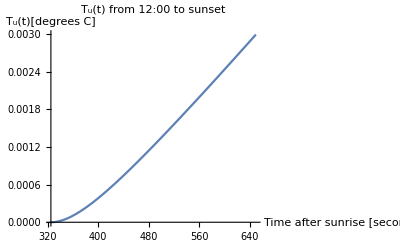

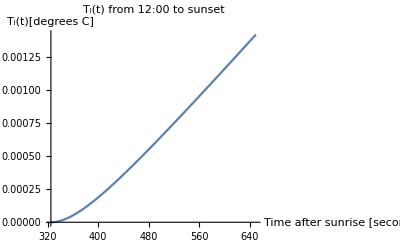

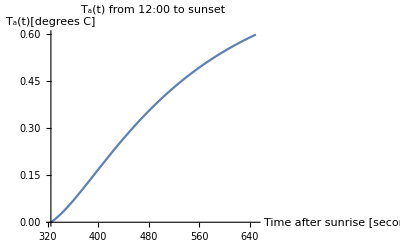

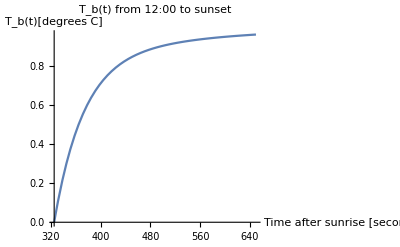

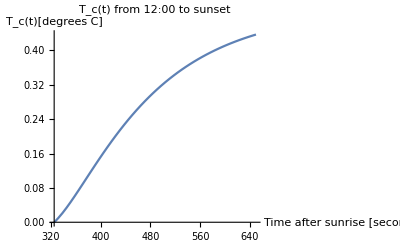

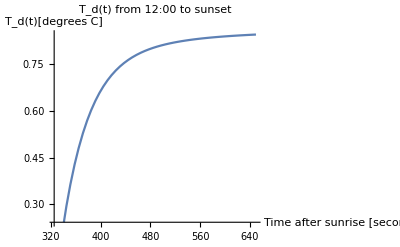

```mathematica
Plot[Subscript[T, u][t]/.latefunc,{t,325,650},PlotLabel->"T_u(t) from 12:00 to sunset", AxesLabel-> {"Time after sunrise [seconds]","T_u(t)[degrees C]"}]
Plot[Subscript[T, l][t]/.latefunc,{t,325,650},PlotLabel->"T_l(t) from 12:00 to sunset", AxesLabel-> {"Time after sunrise [seconds]","T_l(t)[degrees C]"}]
Plot[Subscript[T, a][t]/.latefunc,{t,325,650},PlotLabel->"T_a(t) from 12:00 to sunset", AxesLabel-> {"Time after sunrise [seconds]","T_a(t)[degrees C]"}]
Plot[Subscript[T, b][t]/.latefunc,{t,325,650},PlotLabel->"T_b(t) from 12:00 to sunset", AxesLabel-> {"Time after sunrise [seconds]","T_b(t)[degrees C]"}]
Plot[Subscript[T, c][t]/.latefunc,{t,325,650},PlotLabel->"T_c(t) from 12:00 to sunset", AxesLabel-> {"Time after sunrise [seconds]","T_c(t)[degrees C]"}]
Plot[Subscript[T, d][t]/.latefunc,{t,325,650},PlotLabel->"T_d(t) from 12:00 to sunset", AxesLabel-> {"Time after sunrise [seconds]","T_d(t)[degrees C]"}]
```